```mathematica
f[x_]:= Piecewise[{{Sqrt[3]*x,0<=x<=0.5},{Sqrt[3 - (x - 2)^2],0.5<=x<=2}, {Sqrt[-2(x - 3.5)], -3 <= x <=2}, {-0.114 (x - 0.5)^2 +5, -3 <= x <= 6}, {0.5x - 1.4485, 6<=x<=9}}]
```

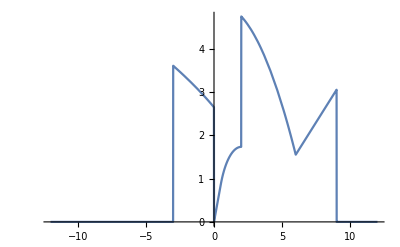

```mathematica
Plot[f[x], {x, -12, 12}]
```

```mathematica
g[x_]:= Piecewise[{{-Sqrt[3]*x,0<=x<=0.5},{-Sqrt[3 - (x - 2)^2],0.5<=x<=2}, {-Sqrt[-2(x - 3.5)], -3 <= x <=2}, {0.114 (x - 0.5)^2 -5, -3 <= x <= 6}, {-0.5x + 1.4485, 6<=x<=9}}]
```

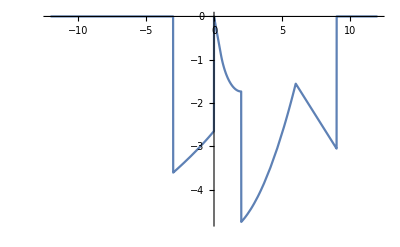

```mathematica
Plot[g[x], {x, -12, 12}]
```

```mathematica
NIntegrate[(f[x]), {x, -3, 9}]
```

32.598

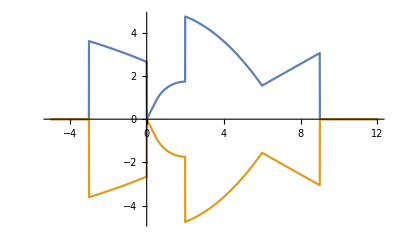

```mathematica
Plot[{f[x], g[x]}, {x, -5, 12}]
```